```mathematica
independetvars={t,x,y,z}
```

{t,x,y,z}

```mathematica
Needs["PlotLegends`"]
Dt[x]//TraditionalForm;
metric[lineelement_,independentvars_List]:=
Block[{lenindependent,differentials,diffmatrix,metricform,varmetric,gh,sum,equation,rule,varhelp,zeros,zerorule},

(*---determine the no. of independent variables---*)
lenindependent=Length[independentvars];

(*---create the differentials corresponding to dx,dt...---*)
differentials=Map[Dt,independentvars];

(*---a mtrix of a differential products---*)
diffmatrix=Outer[Times,differentials, differentials];

(*---the general matrix form---*)
metricform=Array[gh,{lenindependent,lenindependent}];

(*---the general metric form---*)
varmetric=Variables[metricform];

(*---build a system of equations to determine the elements of the metric---*)
If[Length[metricform]==Length[diffmatrix],
sum=0;
Do[
Do[
sum=sum+metricform[[i,j]] diffmatrix[[i,j]],
{j,1,lenindependent}],
{i,1,lenindependent}],
sum=0
];

(*---construct the metric tensor---*)
If[sum===0,
Return[sum],
sum=sum-lineelement;
equation=CoefficientList[sum,differentials]==0;
rule=Solve[equation,varmetric];
metricform=metricform/.rule;
varmetric=Variables[metricform];

(*---replace the nonzero elements---*)
varhelp={};
Do[
If[Not[FreeQ[varmetric[[i]],gh]],
AppendTo[varhelp,varmetric[[i]] ]
],
{i,1,Length[varmetric]}];
zeros=Table[0,{Length[varhelp]}];
SubstRule[x_,y_]:=x->y;
zerorule=Thread[SubstRule[varhelp,zeros]];
metricform=Flatten[metricform/.zerorule,1];

(*---make the metricform symmtric---*)
metricform=Expand[(metricform+Transpose[metricform])/2]
];
metricform
];
Off[Solve::svars];
Off1[Solve:: svars];
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
ds2=(1-(2 m r)/(△_1)) Dt[t]^2-(△_1)/(△_2) Dt[r]^2- △_1 Dt[θ]^2-((2 m a^2 r Sin[θ]^2)/(△_1)+r^2+a^2) Sin[θ]^2 Dt[ϕ]^2-(4 a m r Sin[θ]^2)/(△_1) Dt[t] Dt[ϕ]
```

Dt[t]^2 (1-(2 m r)/(△_1))-Dt[ϕ]^2 Sin[θ]^2 (a^2+r^2+(2 a^2 m r Sin[θ]^2)/(△_1))-(4 a m r Dt[t] Dt[ϕ] Sin[θ]^2)/(△_1)-Dt[θ]^2 △_1-(Dt[r]^2 △_1)/(△_2)

```mathematica
coords={t,r,θ,ϕ};
n=Length[coords];
gμν=metric[ds2,{t,r,θ,ϕ}];
gμν//MatrixForm
```

(1-(2 m r)/(△_1) | 0 | 0 | -(2 a m r Sin[θ]^2)/(△_1)
0 | -(△_1)/(△_2) | 0 | 0
0 | 0 | -△_1 | 0
-(2 a m r Sin[θ]^2)/(△_1) | 0 | 0 | -a^2 Sin[θ]^2-r^2 Sin[θ]^2-(2 a^2 m r Sin[θ]^4)/(△_1))

```mathematica
inversegμν=Simplify[Inverse[gμν]];
inversegμν//MatrixForm
```

((2 a^2 m r Sin[θ]^2+(a^2+r^2) △_1)/(-m r (a^2+2 r^2+a^2 Cos[2 θ])+(a^2+r^2) △_1) | 0 | 0 | (2 a m r)/(m r (a^2+2 r^2+a^2 Cos[2 θ])-(a^2+r^2) △_1)
0 | -(△_2)/(△_1) | 0 | 0
0 | 0 | -1/(△_1) | 0
(2 a m r)/(m r (a^2+2 r^2+a^2 Cos[2 θ])-(a^2+r^2) △_1) | 0 | 0 | -(Csc[θ]^2 (2 m r-△_1))/(m r (a^2+2 r^2+a^2 Cos[2 θ])-(a^2+r^2) △_1))

```mathematica
a=0;
△_1=r^2+a^2 Cos[θ]^2;
△_2=r^2-2 m r+a^2;
gμν//MatrixForm//Simplify
```

(1-(2 m)/r | 0 | 0 | 0
0 | r/(2 m-r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
(* Conclusion: for zero angular momentum Kerr solution reduces to Schwarzschild solution *)
```

```mathematica
(* Cristoffel symbols *)
a=.;m=.;
△_1=r^2+a^2 Cos[θ]^2;
△_2=r^2-2 m r+a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversegμν[[μ,σ]])*(D[gμν[[σ,ν]],coords[[λ]] ]+D[gμν[[σ,λ]],coords[[ν]] ]-D[gμν[[ν,λ]],coords[[σ]] ]),
{σ,1,n}],{μ,1,n},{ν,1,n},{λ,1,n}] ]
```

```mathematica
listchristoffel:=Table[If[UnsameQ[christoffel[[μ,ν,λ]],0],{Style[Subsuperscript[Γ,Row[{ν-1,λ-1}],μ-1],16],"= ",Style[christoffel[[μ,ν,λ]],17]}],{μ,1,n},{ν,1,n},{λ,1,n}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],3],TableSpacing->{2,2}]
```

Γ_01^0 | =  | -(4 m (a^2+r^2) (-r^2+a^2 Cos[θ]^2))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_02^0 | =  | -(4 a^2 m r Sin[2 θ])/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_10^0 | =  | -(4 m (a^2+r^2) (-r^2+a^2 Cos[θ]^2))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_13^0 | =  | (4 a m (r^2 (a^2+3 r^2)+(-a^4+a^2 r^2) Cos[θ]^2) Sin[θ]^2)/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_20^0 | =  | -(4 a^2 m r Sin[2 θ])/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_23^0 | =  | -(8 a^3 m r Cos[θ] Sin[θ]^3)/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_31^0 | =  | (4 a m (r^2 (a^2+3 r^2)+(-a^4+a^2 r^2) Cos[θ]^2) Sin[θ]^2)/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_32^0 | =  | -(8 a^3 m r Cos[θ] Sin[θ]^3)/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_00^1 | =  | -(m (a^2+r (-2 m+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)
Γ_03^1 | =  | -(a m (a^2+r (-2 m+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ_11^1 | =  | (r (a^2-m r)+a^2 (m-r) Cos[θ]^2)/((a^2+r (-2 m+r)) (r^2+a^2 Cos[θ]^2))
Γ_12^1 | =  | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ_21^1 | =  | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ_22^1 | =  | -(r (a^2+r (-2 m+r)))/(r^2+a^2 Cos[θ]^2)
Γ_30^1 | =  | -(a m (a^2+r (-2 m+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)
Γ_33^1 | =  | -((a^2+r (-2 m+r)) Sin[θ]^2 (r^5+a^4 r Cos[θ]^4-a^2 m r^2 Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 m Sin[θ]^2)))/((r^2+a^2 Cos[θ]^2)^3)
Γ_00^2 | =  | -(2 a^2 m r Cos[θ] Sin[θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ_03^2 | =  | -(a m r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ_11^2 | =  | (a^2 Cos[θ] Sin[θ])/((a^2+r (-2 m+r)) (r^2+a^2 Cos[θ]^2))
Γ_12^2 | =  | r/(r^2+a^2 Cos[θ]^2)
Γ_21^2 | =  | r/(r^2+a^2 Cos[θ]^2)
Γ_22^2 | =  | -(a^2 Cos[θ] Sin[θ])/(r^2+a^2 Cos[θ]^2)
Γ_30^2 | =  | -(a m r (a^2+r^2) Sin[2 θ])/((r^2+a^2 Cos[θ]^2)^3)
Γ_33^2 | =  | -(Cos[θ] Sin[θ] (a^2+r^2+(4 a^2 m r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(2 a^4 m r Sin[θ]^4)/((r^2+a^2 Cos[θ]^2)^2)))/(r^2+a^2 Cos[θ]^2)
Γ_01^3 | =  | (4 a m (-r^2+a^2 Cos[θ]^2))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_02^3 | =  | (8 a m r Cot[θ])/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_10^3 | =  | (4 a m (-r^2+a^2 Cos[θ]^2))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_13^3 | =  | (4 (r^4 (-2 m+r)+a^4 r Cos[θ]^4-a^2 m r^2 Sin[θ]^2+a^2 Cos[θ]^2 (2 r^2 (-m+r)+a^2 m Sin[θ]^2)))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_20^3 | =  | (8 a m r Cot[θ])/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_23^3 | =  | ((3 a^4+8 a^2 m r+8 a^2 r^2+8 r^4+4 a^2 (a^2+2 r (-m+r)) Cos[2 θ]+a^4 Cos[4 θ]) Cot[θ])/(2 (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_31^3 | =  | (4 (r^4 (-2 m+r)+a^4 r Cos[θ]^4-a^2 m r^2 Sin[θ]^2+a^2 Cos[θ]^2 (2 r^2 (-m+r)+a^2 m Sin[θ]^2)))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
Γ_32^3 | =  | ((3 a^4+8 a^2 m r+8 a^2 r^2+8 r^4+4 a^2 (a^2+2 r (-m+r)) Cos[2 θ]+a^4 Cos[4 θ]) Cot[θ])/(2 (a^2+2 r^2+a^2 Cos[2 θ])^2)

```mathematica
(* Geodesic equations *)
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]'coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
listgeodesic:=Table[{"d/dt"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
TableForm[listgeodesic,TableSpacing->{2}]
```

d/dt t' | = | (8 m (a^2 r (a^2+r (-2 m+r)) Sin[2 θ] θ' (t'+a Sin[θ]^2 ϕ')+r' (1/2 (a^2+r^2) (a^2-2 r^2+a^2 Cos[2 θ]) t'+a (-r^2 (a^2+3 r^2)+a^2 (a^2-r^2) Cos[θ]^2) Sin[θ]^2 ϕ')))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)
d/dt r' | = | (-((r^2+a^2 Cos[θ]^2)^2 (r (a^2-m r)+a^2 (m-r) Cos[θ]^2) (r')^2)/(a^2+r (-2 m+r))+m (a^2+r (-2 m+r)) (-r^2+a^2 Cos[θ]^2) (t')^2+2 a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] r' θ'+r (a^2+r (-2 m+r)) (r^2+a^2 Cos[θ]^2)^2 (θ')^2+2 a m (a^2+r (-2 m+r)) (-r^2+a^2 Cos[θ]^2) Sin[θ]^2 t' ϕ'+(a^2+r (-2 m+r)) Sin[θ]^2 (r^5+a^4 r Cos[θ]^4-a^2 m r^2 Sin[θ]^2+Cos[θ]^2 (2 a^2 r^3+a^4 m Sin[θ]^2)) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dt θ' | = | (-(a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (r')^2)/(a^2+r (-2 m+r))+a^2 m r Sin[2 θ] (t')^2-2 r (r^2+a^2 Cos[θ]^2)^2 r' θ'+a^2 Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (θ')^2+2 a m r (a^2+r^2) Sin[2 θ] t' ϕ'+Cos[θ] (r^2+a^2 Cos[θ]^2)^2 Sin[θ] (a^2+r^2+(4 a^2 m r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(2 a^4 m r Sin[θ]^4)/((r^2+a^2 Cos[θ]^2)^2)) (ϕ')^2)/((r^2+a^2 Cos[θ]^2)^3)
d/dt ϕ' | = | -((a^2+r (-2 m+r)) Cot[θ] θ' (16 a m r t'+(3 a^4+8 a^2 m r+8 a^2 r^2+8 r^4+4 a^2 (a^2+2 r (-m+r)) Cos[2 θ]+a^4 Cos[4 θ]) ϕ')+2 r' (4 a m (-r^2+a^2 Cos[θ]^2) t'+(-8 m r^4+4 r^5-8 a^2 (m-r) r^2 Cos[θ]^2+4 a^4 r Cos[θ]^4-4 a^2 m r^2 Sin[θ]^2+a^4 m Sin[2 θ]^2) ϕ'))/((a^2+r (-2 m+r)) (a^2+2 r^2+a^2 Cos[2 θ])^2)

```mathematica
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=gμν;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],
Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]] [0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,maxτi}];
soln]
uinvar=1;
```

```mathematica
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln;
ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
```

```mathematica
udotu[solni_,τval_]:=Block[{xα,uα},
xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten;
uα=D[xα,τ];
xα=xα/.τ->τval;
uα=uα/.τ->τval;
uα.((gμν/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
```

```mathematica
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

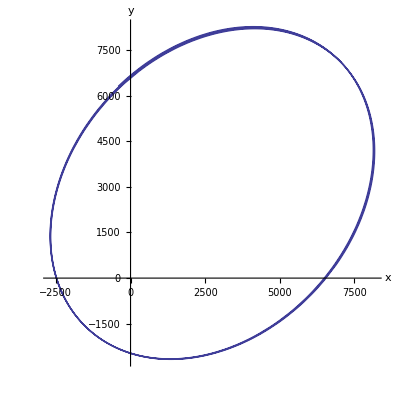

1.00024×10^7

|  |  | u.u values
τ= | 0 | → | 1.
τ= | 2000000 | → | 1.
τ= | 4000000 | → | 1.
τ= | 6000000 | → | 1.
τ= | 8000000 | → | 1.
τ= | 10000000 | → | 1.

```mathematica
(* 2D plot *)
m=1;a=0.99 m;
maxτ=10000000;
soln=computeSoln[maxτ,{0,0,0.0000006},{0,10000,π/2, Pi/4}];
xyzsoln=sphslnToCartsln[soln];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y}]
Subscript[t, final]=First[(t[τ]/.soln)/.τ->maxτ]
Join[{{"","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

```mathematica
m=1;a=0;rplus=m+Sqrt[m^2-a^2];
maxτ=2000;
ivs={0,0,0.088};
ics={0,6.5,π/2,1};
soln=computeSoln[maxτ,ivs,ics];
xyzsoln=sphslnToCartsln[soln];
SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0,2 Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->5000];
Show[%,%%,DisplayFunction->$DisplayFunction,PlotRange->{{-20,20},{-20,20},{-20,20}}]
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"Proper Time","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

-Graphics3D-

Final Coordinates:
t = 2389.72
r = 7.27271
θ = 1.5708
ϕ = 76.5173

Proper Time |  |  | u.u values
τ= | 0 | → | 1.
τ= | 400 | → | 1.
τ= | 800 | → | 1.
τ= | 1200 | → | 1.
τ= | 1600 | → | 1.
τ= | 2000 | → | 1.

```mathematica
m=1;a=0.99;rplus=m+Sqrt[m^2-a^2];
maxτ=5000;
ivs={-0.08,-0.035,0.0359};
ics={0,10,π/4,.2};
soln=computeSoln[maxτ,ivs,ics];
xyzsoln=sphslnToCartsln[soln];
SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0,2 Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->5000];
Show[%,%%,DisplayFunction->$DisplayFunction,PlotRange->{{-40,40},{-40,40},{-40,40}}]
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"Proper Time","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

-Graphics3D-

Final Coordinates:
t = 5409.25
r = 30.4467
θ = 1.82669
ϕ = 57.1167

Proper Time |  |  | u.u values
τ= | 0 | → | 1.
τ= | 1000 | → | 1.
τ= | 2000 | → | 1.
τ= | 3000 | → | 1.
τ= | 4000 | → | 1.
τ= | 5000 | → | 1.

```mathematica
m=1;a=0;rplus=m+Sqrt[m^2-a^2];
maxτ=5000;
ivs={-0.08,-0.035,0.0359};
ics={0,10,π/4,.2};
soln=computeSoln[maxτ,ivs,ics];
xyzsoln=sphslnToCartsln[soln];
SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0,2 Pi},DisplayFunction->Identity];
ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotPoints->5000];
Show[%,%%,DisplayFunction->$DisplayFunction,PlotRange->{{-40,40},{-40,40},{-40,40}}]
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"Proper Time","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

-Graphics3D-

Final Coordinates:
t = 5428.87
r = 27.556
θ = 1.30022
ϕ = 62.6849

Proper Time |  |  | u.u values
τ= | 0 | → | 1.
τ= | 1000 | → | 1.
τ= | 2000 | → | 1.
τ= | 3000 | → | 1.
τ= | 4000 | → | 1.
τ= | 5000 | → | 1.